```mathematica
(* Common *)
On[Assert]
comment[c_][val_]:=(Print[c]; val);
atNotebook[path_]:=FileNameJoin[{NotebookDirectory[],path}];
Second[xs_]:=xs[[2]];

sanityCheck[]:=
Map[Block[{h=#},
Print["Testing "<>ToString[h]];
Assert[m0[h]≥0,"Negative mass"];
Assert[Γ0[h]≥0,"Negative width"];
Assert[Sum[dec[[2]],{dec,decays[h]}]==1.,"Incomplete branching ratios for "<>ToString[h]];
Assert[2isoSpin[h]∈Integers,"Isospin is not half-integer for "<>ToString[h]];
Map[Module[{j1,j2,jOut,lChan,inRange,outRange},
j1=j@#[[1,1]];j2=j@#[[1,2]];jOut=j@h;lChan=#[[3]];
inRange=Range[Abs[j1-j2],Abs[j1+j2]];
outRange=Range[Abs[jOut-lChan],Abs[jOut+lChan]];
Assert[IntersectingQ[inRange,outRange],"Angular momenta inaccessible for "<>ToString[h]<>"-->"<>ToString[#[[1]]]];
]&,decays[h]];
True
]&,Join[Ns,Ds,Ms]];


(* Kinematic and helper functions *)
ClearAll[BR]; ClearAll[massDecayBound];
getDecay[hIn_,hOuts_]:=SelectFirst[decays[hIn],#[[1]]==hOuts&];
BR[hIn_,hOuts_]:=Block[{dec=getDecay[hIn,hOuts]},If[MissingQ[dec],0,dec[[2]]]];
decayAngularMomentum[hIn_,hOuts_]:=getDecay[hIn,hOuts][[3]];
decayProducts[particle_]:=First/@decays[particle];
minMass[particle_]:=If[Γ0[particle]==0.,m0[particle],0.];
massDecayBound[particle_]:=massDecayBound[particle]=
Min[(Total[minMass/@First[#]]&) /@ decays[particle]];

pCMS[eCM_,mA_,mB_]:=If[eCM≤mA+mB,0,1/(2.eCM)*Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]];

psSize[mDistribution_][eCM_,{hA_,hB_},lFac_:0]:=Module[{m0A,m0B},
m0A=m0[hA];m0B=m0[hB];
If[Γ0[hA]==Γ0[hB]==0.,
If[eCM<m0A+m0B,Return[0],Return@(pCMS[eCM,m0A,m0B]^lFac)]
];
If[Γ0[hA]==0.,
If[eCM<m0A,Return[0],
Return@NIntegrate[pCMS[eCM,m0A,mB]^lFac mDistribution[hB,mB],{mB,massDecayBound[hB],eCM-m0A}, PrecisionGoal->3,AccuracyGoal->10]
]];
If[Γ0[hB]==0.,
If[eCM<m0B,Return[0],
Return@NIntegrate[pCMS[eCM,mA,m0B]^lFac mDistribution[hA,mA],{mA,massDecayBound[hA],eCM-m0B}, PrecisionGoal->3,AccuracyGoal->10]
]];
NIntegrate[pCMS[eCM,mA,mB]^lFac mDistribution[hA,mA]mDistribution[hB,mB],{mA,massDecayBound[hA],eCM},{mB,massDecayBound[hB],eCM-mA}, PrecisionGoal->3,AccuracyGoal->10]
];

ClearAll[a0];
breitWigner[Γ0_Real,dm_Real]:=Γ0/(dm^2+0.25Γ0^2)
a0[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a0: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ0[particle],m0[particle]-m]/(2Pi)
];
p0Mean=psSize[a0];
ClearAll[p0MeanCh];
p0MeanCh[m0_,{hA_,hB_},lFac_]:=p0MeanCh[m0,{hA,hB},lFac]=p0Mean[m0,{hA,hB},lFac];

ClearAll[Γ];
Γ[hIn_,hOuts_,m_Real]:= Module[{br,p0,p0res,p01,p0res1,lChan},
If[m≤Sum[minMass[h],{h,hOuts}],Return[0]];
br=BR[hIn,hOuts];
If[br==0,Return[0]];
lChan=decayAngularMomentum[hIn,hOuts];

p01=p0Mean[m,hOuts,2lChan+1];
p0res1= p0MeanCh[m0[hIn],hOuts,2lChan+1];
p0=p0Mean[m,hOuts,2lChan]; 
p0res=p0MeanCh[m0[hIn],hOuts,2lChan];

Assert[p0res>0];Assert[p0res1>0];
Γ0[hIn] br* m0[hIn]/m * (p01/p0res1) * 1.2/(1. + 0.2(p0/p0res))
];
Γ[h_,m_]:=Sum[Γ[h,decs,m],{decs,decayProducts[h]}];


(* Define the mass distribution function and <p> *)
ClearAll[aN]; ClearAll[a];
aN[particle_]:=comment["Calculating aN for "<>ToString[particle],
aN[particle]=Re@NIntegrate[breitWigner[Γ[particle,m],m0[particle]-m],{m,massDecayBound[particle],Infinity}]
];

a[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
If[m≤0,0,breitWigner[Γ[particle,m],m0[particle]-m]/aN[particle]]
];
pMean=psSize[a];

pLab[mA_,mB_,eCM_]:=If[eCM≤mA+mB,0,Sqrt[(eCM^2-mA^2-mB^2)^2/(4mB^2) - mA^2]];
```

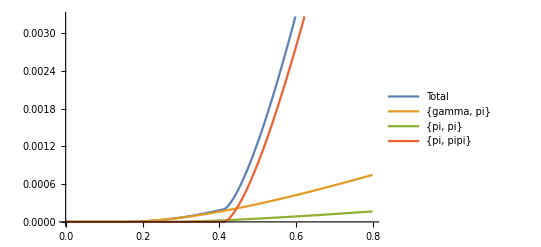

```mathematica
Block[{h=omega},
Plot[Evaluate@Flatten@{
Γ[h,m],
Table[Γ[h,outs,m],{outs,decayProducts[h]}]
},{m,0.,m0[h]+2Γ0[h]},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]}]
]
```

```mathematica
Module[{lBound,rBound},
lBound=Max[0.,Min@Table[m0[mes]-4Γ0[mes],{mes,Ms}]];
rBound=Max@Table[m0[mes]+4Γ0[mes],{mes,Ms}];
Plot[Evaluate@Table[a[mes,m],{mes,Ms}],{m,lBound,rBound},PlotRange->All]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.779067}. NIntegrate obtained 6.32659 and 0.0000517053 for the integral and error estimates.

Calculating aN for omega

Calculating aN for rho

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.982712}. NIntegrate obtained 7.10744 and 0.00158113 for the integral and error estimates.

Calculating aN for Kstar

$Aborted

```mathematica
decayAngularMomentum[f0980,{Ka,Ka}]
```

0

```mathematica
Table[a[mes,5.],{mes,Ms}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.982712}. NIntegrate obtained 7.10744 and 0.00158113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.987825}. NIntegrate obtained 6.44157 and 0.000208627 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {284.088}. NIntegrate obtained 6.70827 and 0.000114871 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Calculating aN for K11270

Calculating aN for a11260

Calculating aN for f1

Calculating aN for f11510

Calculating aN for K21430

Calculating aN for a21320

Calculating aN for f21270

Calculating aN for f21525

Calculating aN for K11400

Calculating aN for b11235

Calculating aN for h11170

Calculating aN for h11380

Calculating aN for Kstar1410

Calculating aN for rho1465

Calculating aN for omega1419

Calculating aN for phi1680

Calculating aN for Kstar1680

Calculating aN for rho1700

Calculating aN for omega1662

Calculating aN for phi1900

{0.000459535,0.00728752,0.00466619,0.00377757,0.000811026,0.00435494,0.00279068,0.00290521,0.00495877,0.00843058,0.00148401,0.0137045,0.00899012,0.00902353,0.012551,0.00694226,0.00400739,0.00381929,0.00958805,0.00836855,0.0182131,0.0171305,0.0131481,0.0150301,0.0219977,0.0160923,0.0201106,0.031267}

```mathematica
pMean[2.,{Ka,Ka},1]
```

0.867177

```mathematica
Γ[f0980,{Ka,Ka},2.]
```

0.410562

```mathematica
pts=Monitor[
Table[
{mes,Table[{resMass,a[mes,resMass]},{resMass,0.,3.,0.001}]},
{mes,Ms}
],{mes,ProgressIndicator[resMass,{0.,3.}]}
];
ListLinePlot[Second/@pts,PlotRange->{0,All},PlotLegends->First/@pts]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.982712}. NIntegrate obtained 7.10744 and 0.00158113 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Length[pts[[1,2]]]
```

3001

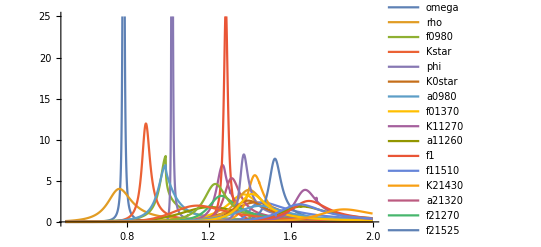

```mathematica
ListLinePlot[Evaluate@Table[pt[[2]][[500;;2000]],{pt,pts}],PlotRange->{0,25},PlotLegends->First/@pts]
```

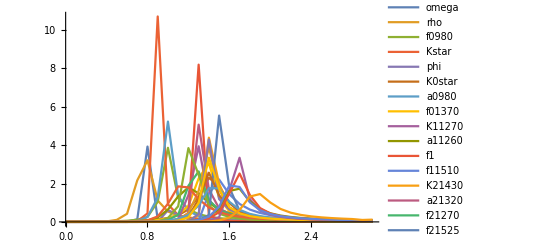

```mathematica
Range
```

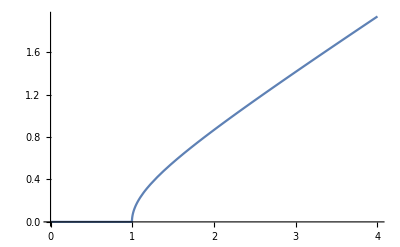

```mathematica
Plot[p0Mean[eCM,{Ka,Ka},1],{eCM,0.,4.}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.982712}. NIntegrate obtained 7.10744 and 0.00158113 for the integral and error estimates.

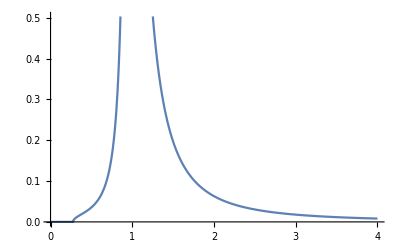

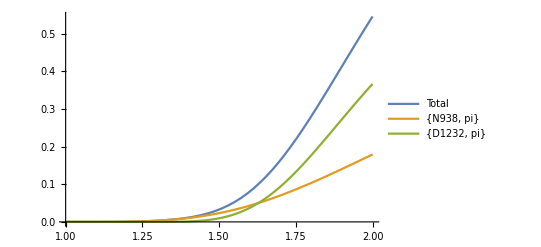

```mathematica
Plot[a[f0980,m],{m,0.,4.}]
```

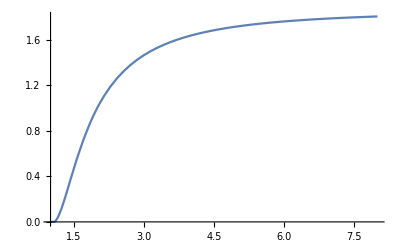

```mathematica
Plot[Evaluate@Table[Γ[D1232,outs,m],{outs,decayProducts@D1232}],{m,1.,8.},PlotRange->All]
```

```mathematica
decayProducts[D1232]
```

{{N938,pi}}

{0.00203,0.02214,0.05117,0.08554,0.12347,0.16361,0.20484,0.24627,0.28718,0.32701,0.36536,0.40197,0.43666,0.46936,0.50004,0.52872,0.55547,0.58038,0.60353,0.62503,0.64499,0.66352,0.68072,0.69669,0.71152,0.72530,0.73812,0.75005,0.76116,0.77152,0.78119,0.79022,0.79866,0.80656,0.81396,0.82089,0.82741,0.83352,0.83928,0.84469,0.84979,0.85460,0.85914,0.86343,0.86749,0.87133,0.87496,0.87841,0.88168,0.88478,0.88773,0.89053,0.89320,0.89574,0.89816,0.90047,0.90267,0.90477,0.90678,0.90870,0.91053,0.91229,0.91397,0.91559,0.91713,0.91861,0.92004,0.92140,0.92272,0.92398,0.92519,0.92636,0.92748,0.92857,0.92961,0.93061,0.93158,0.93252}

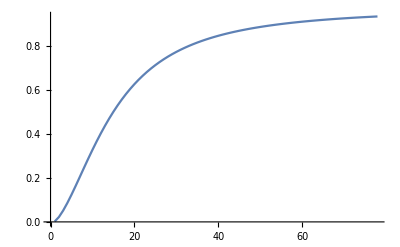

```mathematica
pts=Table[Γ[rho,m],{m,0.3,8.,0.1}];
NumberForm[#,{6,5}]&/@pts
ListLinePlot[pts]
```

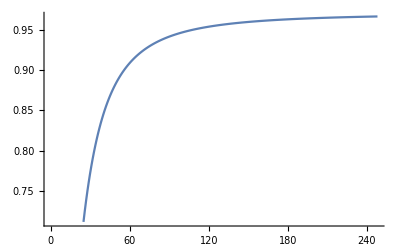

```mathematica
ListLinePlot[pts]
```